# Computation Explorations with physical quantities

Peter Cullen Burbery

I decided to take a look at various neat examples for functions for physical quantities. I am creating a computational exploration with physical quantities.

## Physical Quantity Lookup

Find all physical quantities with the same dimensions as ohms:

Use the resource function PhysicalQuantityLookup:

```mathematica
PersistResourceFunction["PhysicalQuantityLookup"]
```

Success[…]

```mathematica
PhysicalQuantityLookup["Ohms"]
```

{AC resistance,DC resistance,electric resistance,internal winding resistance,resistive load,electric surface resistance,cable impedance,characteristic electric impedance,electric alternating current resistance,electric differential resistance,electric impedance,electric impedance modulus,electric mutual resistance,electric reactance,impedance load,inductor impedance,magnetic inductance rate,magnetic memristance,magnetoelectric coefficient dE/dH,transformer sensitivity}

Look for physical quantities that cover a quantity:

```mathematica
PhysicalQuantityLookup[Quantity[, ("Meters")^4]]
```

{area moment of inertia x,area moment of inertia y,axial area moment of inertia,planar area moment of inertia,polar area moment of inertia,product area moment of inertia,transformer area product}

Look up physical quantities with the dimensions of power:

```mathematica
PhysicalQuantityLookup[Quantity[, "Terawatts"]]
```

{power,energy flux,electric power,energy flow rate,heat flow rate,real power,active power,battery energy self-discharge rate,bolometric luminosity,tonnage rating,dietary energy intake rate,electric apparent power,electric complex power,electric non-active power,electric reactive power,energy consumption rate,energy production rate,input power,Larmor power,livestock carrying capacity,luminosity,mechanical power,output power,radiant power,solar panel electric output power,solar power,sound power,stellar luminosity,tidal power,vacuum pump leakage rate,wave power,wind power}

I first need to store my resource function PhysicalQuantityData:

```mathematica
PersistResourceFunction["PhysicalQuantityData"]
```

Success[…]

Group physical quantities by their base physical quantity:

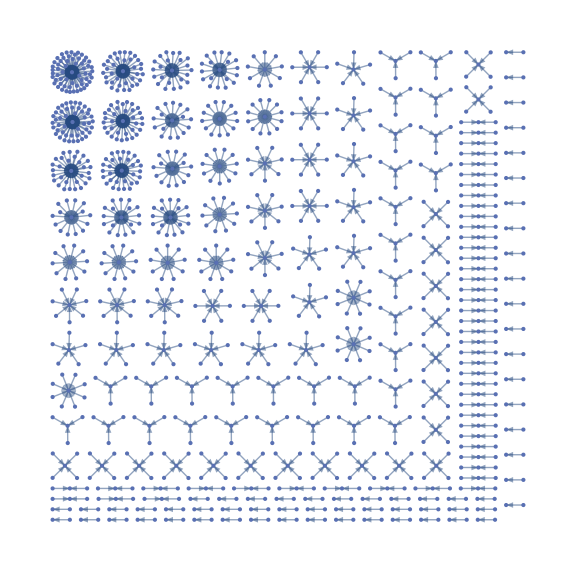

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Large]
```

Group by  SI unit:

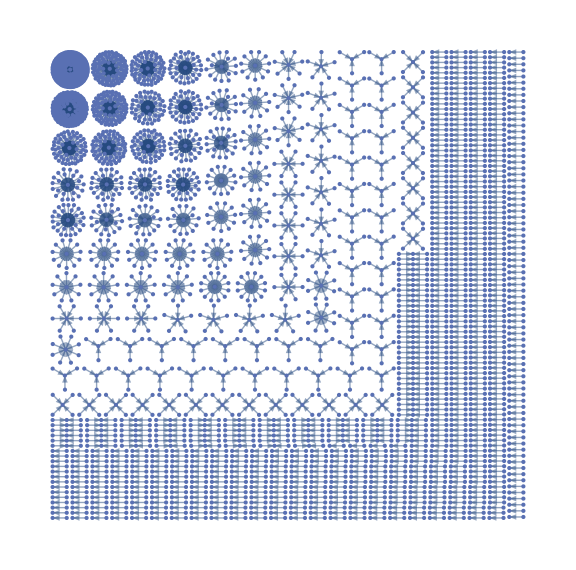

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","SIUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Large]
```

```mathematica
Entity["PhysicalQuantity","TransmissionCoefficient"]["Dataset"]
```

```mathematica
Entity["PhysicalQuantity","TransmissionCoefficient"]["PropertyAssociation"]
```

<|abbreviations→Missing[NotAvailable],algebraic types→{scalar},alternate names→Missing[NotAvailable],base physical quantity→Missing[NotAvailable],canonical unit→1 U,classes→{},dimensions→{},entity classes→{},instances→Missing[NotApplicable],name→transmission coefficient,named SI unit→Missing[None],physical property type→Missing[NotAvailable],quantity variable→T TransmissionCoefficient,SI base unit→1 U,SI unit→1 U,standard identifiers→<|Wikidata→Q75384|>,standard symbols→<||>,symbols→{}|>

Group by SI base unit:

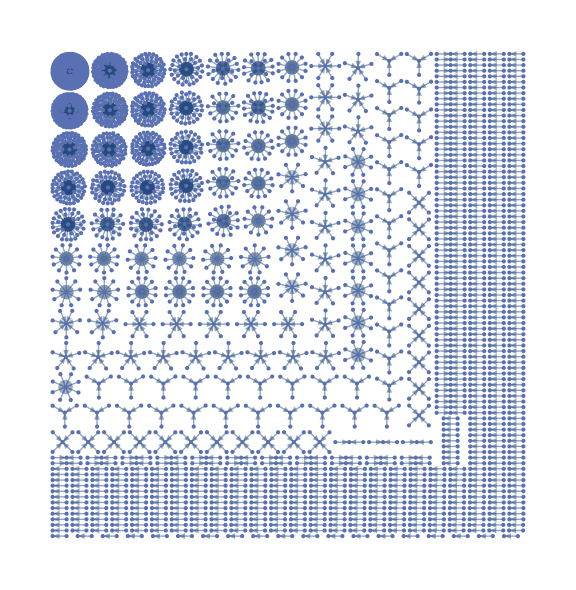

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","SIBaseUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Large]
```

Group by total ab